```mathematica
1.Naloga

trikotnik={{0,0},{0,1},{1,0}} (*(0,0)=A, (0,5)=B, (7,4)=C*)
stranice[{AA_,BB_,CC_}]:={{BB,CC},{CC,AA},{AA,BB}}
koti[{AA_,BB_,CC_}]:={{CC,AA,BB},{AA,BB,CC},{BB,CC,AA}}
```

1. Naloga

{{0,0},{0,1},{1,0}}

```mathematica
stranice[trikotnik]
```

{{{0,0},{0,5}},{{0,5},{7,4}},{{7,4},{0,0}}}

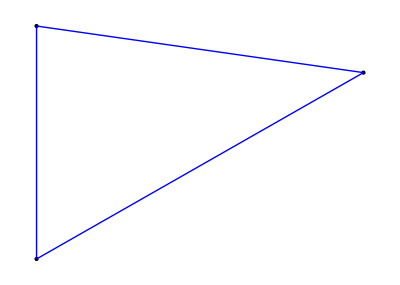

```mathematica
SlikaOglisc[trikotnik_] := Map[Point, trikotnik];
SlikaStranic[trikotnik_] := Map[Line, stranice[trikotnik]];
NarisiTrikotnik[trikotnik_] := Graphics[
{PointSize[Large], SlikaOglisc[trikotnik], {Blue, SlikaStranic[trikotnik]}}, AspectRatio -> Automatic
]
NarisiTrikotnik[trikotnik]
```

```mathematica
2. Naloga
```

```mathematica
VektorSimetraleKota[{x_,y_,z_}]:= Normalize[Normalize[z-y]+Normalize[x-y]]
```

```mathematica
SimetralaKota[{x_, y_, z_}, dol_:2] := {y,y+VektorSimetraleKota[{x,y,z}]*dol}
```

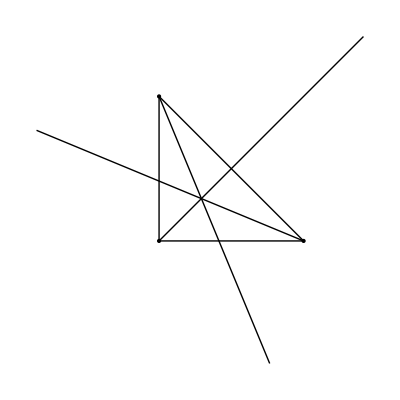

```mathematica
SlikaSimetralKotov[trikotnik_] := Map[Line, Map[SimetralaKota, koti[trikotnik]]];
ClearAll[NarisiTrikotnik]

NarisiTrikotnik[trikotnik_, OptionsPattern[Simetrale->False]]:= Module[{slike}, slike={ PointSize[Large], SlikaOglisc[trikotnik],SlikaStranic[trikotnik] };
If[OptionValue[Simetrale]==True, AppendTo[slike, SlikaSimetralKotov[trikotnik]]];
Graphics[slike, AspectRatio->Automatic]]
NarisiTrikotnik[trikotnik,Simetrale->True]
```

4. Naloga

```mathematica
ClearAll[NarisiTrikotnik]
```

```mathematica
PresecisceSimetral[{AA_,BB_,CC_}]:= Module[{presecisce},
presecisce= SimetralaKota[trikotnik]=={x,y};

]
```

```mathematica
Simplify[PresecisceSimetral]
```

PresecisceSimetral